```mathematica
$Assumptions={t∈Reals}
```

{t∈ℝ}

2D Example

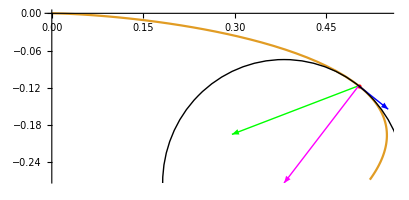

```mathematica
(*Curve in 2D space*)
r={Cos[t]t^2,Sin[t]-t};
rp=D[r,t];
rpp=D[r,t,t];

(*Get 3D vector from 2D vector*)
v3[vec_]:=Flatten[{vec,0}];

(*Normal vector on curve*)
n=Normalize[(v3[rp]×v3[rpp])×v3[rp]]⟦{1,2}⟧;

(*Curvature*)
κ=Norm[Cross[v3[rp],v3[rpp]]]/Norm[v3[rp]]^3;
ρ=1/κ;

(*Plot the graph*)
point=0.9;
pltCurve=ParametricPlot[r,{t,0,1.2}];
pltPoint=Graphics[{Red,Point[r/.t->point]}];
pltp=Graphics[{Blue,Arrow[{r,r+0.1rp}/.t->point]}];
pltpp=Graphics[{Green,Arrow[{r,r+0.1rpp}/.t->point]}];
pltn=Graphics[{Magenta,Arrow[{r,r+ρ n}/.t->point]}];
pltCircle=Graphics[{Black,Circle[r+ρ n/.t->point,ρ/.t->point]}];
Show[pltCurve,pltPoint,pltp,pltpp,pltn,pltCircle,AspectRatio->Automatic]
```

Example 3D
Curvature (https://de.wikipedia.org/wiki/Kr%C3%BCmmung?veaction=edit&section=6#Raumkurven)
κ=(|r'×r''|)/(|r'|.b3)

```mathematica
(*Curve in 2D space*)
r={Cos[t]t^2,Sin[t]-t,Cos[t]Sin[t]};
rp=D[r,t];
rpp=D[r,t,t];

(*Normal vector on curve*)
n=Normalize[(rp×rpp)×rp];

(*Normalize tangent*)
tn=Normalize[rp];

(*Plot the graph*)
point=1.1;
pltCurve=ParametricPlot3D[r,{t,0,1.2}];
pltPoint=Graphics3D[{Red,Point[r/.t->point]}];
pltp=Graphics3D[{Blue,Arrow[{r,r+0.1rp}/.t->point]}];
pltpp=Graphics3D[{Green,Arrow[{r,r+0.1rpp}/.t->point]}];
pltn=Graphics3D[{Magenta,Arrow[{r,r+ρ n}/.t->point]}];
pltCircle=ParametricPlot3D[r+ρ(n+Sin[ϕ]tn+Cos[ϕ]n)/.t->point,{ϕ,-30,0.3},PlotStyle->Black];
Show[pltCurve,pltPoint,pltp,pltpp,pltn,pltCircle,PlotRange->All,AspectRatio->Automatic]
```

-Graphics3D-